# Self Energy

## Load FeynArts and FormCalc

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Quit[]
```

## Photon Polarization

## Set-up

```mathematica
CKM=IndexDelta;
```

```mathematica
process={V[1]} -> {V[1]};
```

```mathematica
name="Photon Polarization";
```

```mathematica
SetOptions[InsertFields,Model->"SM",InsertionLevel->Particles];
SetOptions[Paint,PaintLevel->{Classes},ColumnsXRows->{3,3}];
```

## One-Loop

### Topologies

> Top. 1 ac/bd/cdcd.m, 0 diagrams

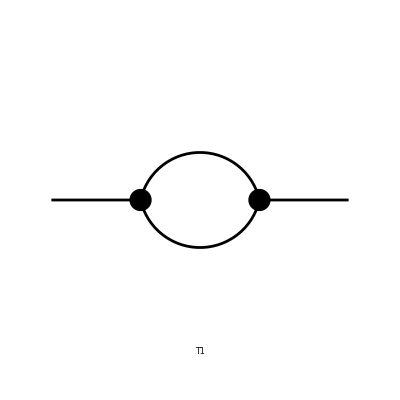

```mathematica
tops1=CreateTopologies[1,1->1,Adjacencies->3,ExcludeTopologies->Tadpoles];
Paint[tops1];
```

### Insertions

```mathematica
ClearProcess[]
```

```mathematica
ins1=InsertFields[tops1, process,QEDOnly];
Paint[ins1,PaintLevel->{Particles}];
```

Excluding 0 Generic, 0 Classes, and 0 Particles fields

InsertFields::extnumber: You cannot fit \!\(\*RowBox[{"1"}]\) -> \!\(\*RowBox[{"2"}]\) external particles onto a \!\(\*RowBox[{"1"}]\) -> \!\(\*RowBox[{"1"}]\) leg topology.

### Feynman Amplitudes

```mathematica
amp1=CreateFeynAmp[ins1,AmplitudeLevel->{Particles}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 9 Particles amplitudes

in total: 9 Particles amplitudes

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{V[1],k1,0,{}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[q1],-1/(16 π^4)ⅈ FeynAmpDenominator[1/(-ME2+(q1)^2),1/(-ME2+(q1-k1)^2)] tr[ME+gs[-(q1)],ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+,ME+gs[-(q1)+k1],ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+] ep[V[1],p1,Lor1] ep^*[V[1],k1,Lor2]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==2,Number==2],Integral[q1],-1/(16 π^4)ⅈ FeynAmpDenominator[1/(-MM2+(q1)^2),1/(-MM2+(q1-k1)^2)] tr[MM+gs[-(q1)],ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+,MM+gs[-(q1)+k1],ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+] ep[V[1],p1,Lor1] ep^*[V[1],k1,Lor2]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==3,Number==3],Integral[q1],-1/(16 π^4)ⅈ FeynAmpDenominator[1/(-ML2+(q1)^2),1/(-ML2+(q1-k1)^2)] tr[ML+gs[-(q1)],ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+,ML+gs[-(q1)+k1],ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+] ep[V[1],p1,Lor1] ep^*[V[1],k1,Lor2]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==4,Number==4],Integral[q1],-1/(16 π^4)ⅈ FeynAmpDenominator[1/(-MU2+(q1)^2),1/(-MU2+(q1-k1)^2)] tr[MU+gs[-(q1)],-2/3 ⅈ EL ga[Lor2].om_--2/3 ⅈ EL ga[Lor2].om_+,MU+gs[-(q1)+k1],-2/3 ⅈ EL ga[Lor1].om_--2/3 ⅈ EL ga[Lor1].om_+] ep[V[1],p1,Lor1] SumOver[Col3,3] ep^*[V[1],k1,Lor2]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==5,Number==5],Integral[q1],-1/(16 π^4)ⅈ FeynAmpDenominator[1/(-MC2+(q1)^2),1/(-MC2+(q1-k1)^2)] tr[MC+gs[-(q1)],-2/3 ⅈ EL ga[Lor2].om_--2/3 ⅈ EL ga[Lor2].om_+,MC+gs[-(q1)+k1],-2/3 ⅈ EL ga[Lor1].om_--2/3 ⅈ EL ga[Lor1].om_+] ep[V[1],p1,Lor1] SumOver[Col3,3] ep^*[V[1],k1,Lor2]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==6,Number==6],Integral[q1],-1/(16 π^4)ⅈ FeynAmpDenominator[1/(-MT2+(q1)^2),1/(-MT2+(q1-k1)^2)] tr[MT+gs[-(q1)],-2/3 ⅈ EL ga[Lor2].om_--2/3 ⅈ EL ga[Lor2].om_+,MT+gs[-(q1)+k1],-2/3 ⅈ EL ga[Lor1].om_--2/3 ⅈ EL ga[Lor1].om_+] ep[V[1],p1,Lor1] SumOver[Col3,3] ep^*[V[1],k1,Lor2]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==7,Number==7],Integral[q1],-1/(16 π^4)ⅈ FeynAmpDenominator[1/(-MD2+(q1)^2),1/(-MD2+(q1-k1)^2)] tr[MD+gs[-(q1)],1/3 ⅈ EL ga[Lor2].om_-+1/3 ⅈ EL ga[Lor2].om_+,MD+gs[-(q1)+k1],1/3 ⅈ EL ga[Lor1].om_-+1/3 ⅈ EL ga[Lor1].om_+] ep[V[1],p1,Lor1] SumOver[Col3,3] ep^*[V[1],k1,Lor2]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==8,Number==8],Integral[q1],-1/(16 π^4)ⅈ FeynAmpDenominator[1/(-MS2+(q1)^2),1/(-MS2+(q1-k1)^2)] tr[MS+gs[-(q1)],1/3 ⅈ EL ga[Lor2].om_-+1/3 ⅈ EL ga[Lor2].om_+,MS+gs[-(q1)+k1],1/3 ⅈ EL ga[Lor1].om_-+1/3 ⅈ EL ga[Lor1].om_+] ep[V[1],p1,Lor1] SumOver[Col3,3] ep^*[V[1],k1,Lor2]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==9,Number==9],Integral[q1],-1/(16 π^4)ⅈ FeynAmpDenominator[1/(-MB2+(q1)^2),1/(-MB2+(q1-k1)^2)] tr[MB+gs[-(q1)],1/3 ⅈ EL ga[Lor2].om_-+1/3 ⅈ EL ga[Lor2].om_+,MB+gs[-(q1)+k1],1/3 ⅈ EL ga[Lor1].om_-+1/3 ⅈ EL ga[Lor1].om_+] ep[V[1],p1,Lor1] SumOver[Col3,3] ep^*[V[1],k1,Lor2]]]

### FormCalc results

```mathematica
ClearProcess[]
```

```mathematica
results1=CalcFeynAmp[amp1]//Simplify
```

preparing FORM code in /home/riccardo/fc-amp-27.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{V[1],k[2],0,{}}}][1/(3 π)Alfa Pair1 (A0[MB2]+A0[MD2]+3 A0[ME2]+3 A0[ML2]+3 A0[MM2]+A0[MS2]+4 (A0[MC2]+A0[MT2]+A0[MU2])-6 (B0i[bb00,0,ME2,ME2]+B0i[bb00,0,ML2,ML2]+B0i[bb00,0,MM2,MM2])-2 (B0i[bb00,0,MB2,MB2]+B0i[bb00,0,MD2,MD2]+B0i[bb00,0,MS2,MS2])-8 (B0i[bb00,0,MC2,MC2]+B0i[bb00,0,MT2,MT2]+B0i[bb00,0,MU2,MU2]))]

```mathematica
UVDivergentPart[results1]//Simplify
```

Amp[{{V[1],k[1],0,{}}}→{{V[1],k[2],0,{}}}][0]

```mathematica
Abbr[]
```

{Pair1→Pair[e[1],ec[2]]}

```mathematica
Subexpr[]
```

{}

## Muon Self-Energy

## Set-up

```mathematica
CKM=IndexDelta;
```

```mathematica
process={F[2,{2}]} -> {F[2,{2}]};
```

```mathematica
name="Muon Self-Energy";
```

```mathematica
SetOptions[InsertFields,Model->"SM",InsertionLevel->Particles];
SetOptions[Paint,PaintLevel->{Classes},ColumnsXRows->{3,3}];
```

## One-Loop

### Topologies

```mathematica
tops1=CreateTopologies[1,1->1,Adjacencies->3,ExcludeTopologies->Tadpoles];
Paint[tops1];
```

> Top. 1 ac/bd/cdcd.m, 0 diagrams

-Graphics-

### Insertions

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ac/bd/cdcd.m, 0 diagrams

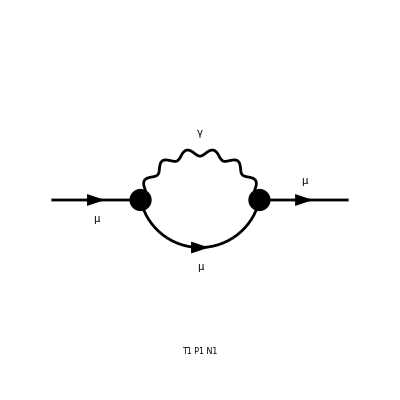

```mathematica
ins1=InsertFields[tops1, process, QEDOnly];
Paint[ins1,PaintLevel->{Particles}];
```

### Feynman Amplitudes

```mathematica
amp1=CreateFeynAmp[ins1,AmplitudeLevel->{Particles}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

FeynAmpList[Process→{{F[2,{2}],p1,MM,{-Charge,LeptonNumber}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[q1],-1/(16 π^4)ⅈ ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).(MM+gs[q1]).(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).u[p1,MM] FeynAmpDenominator[1/(-MM2+(q1)^2),1/(q1-k1)^2] g[Lor1,Lor2]]]

### FormCalc results

```mathematica
ClearProcess[]
```

```mathematica
result1=CalcFeynAmp[amp1,OnShell->True]//Simplify
```

preparing FORM code in /home/riccardo/fc-amp-27.frm

running FORM...

ok

Amp[{{F[2,{2}],k[1],MM,{-Charge,LeptonNumber}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}}}][(Alfa (F1+F2) MM (Finite-2 B0i[bb0,MM2,0,MM2]+2 B0i[bb1,MM2,0,MM2]))/(4 π)]

```mathematica
UVDivergentPart[result1]//Simplify
```

Amp[{{F[2,{2}],k[1],MM,{-Charge,LeptonNumber}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}}}][-(3 Alfa Divergence (F1+F2) MM)/(4 π)]

```mathematica
Abbr[]
```

{F1→(u̇ 2|6|u1),F2→(u̇ 2|7|u1)}

```mathematica
??Simplify
```

```mathematica
??FullSimplify
```